```mathematica
Print["Iteration          Values"]
f[x_]:=x^3-x-1;x0=2.0;n=1;tol=0.0001;
x1=x0-f[x0]/f'[x0];error=x0-x1;
While[Abs[error]>tol,x1=x0-f[x0]/f'[x0];error=x0-x1;
Print["    ",n,"            ",PaddedForm[x1,{7,5}]];n++;x0=x1]
Print["Hence the real root is = ",x1]
```

Iteration          Values

1              1.54545

2              1.35961

3              1.32580

4              1.32472

5              1.32472

Hence the real root is = 1.32472

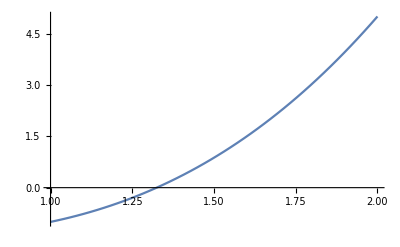

```mathematica
Plot[f[x],{x,1,2}]
```